```mathematica
bdir="~/Software/BOS/build/";
```

```mathematica
GetSnapshot[n_]:=ReadList[bdir<>"snapshot_"<>ToString[n]<>".dat",{Number,Number,Number,Number,Number,Number}]
```

```mathematica
nn=Length[FileNames[bdir<>"snapshot_*"]];
```

```mathematica
GetSnapshot[7]
```

{{0.875183,1.24837,2,0.875183,1.24837,2},{4,3.17749,2.16574,4.07663,3.42545,2.47232},{2.66126,1,3.30873,2.61547,0.95337,3.12012},{3.24487,1.20156,3,3.78198,1.25536,2.01331},{3,2.18935,2.804,3.10422,2.2742,2.99533},{3.32139,1.60701,4.17923,3.4756,1.76058,4.01272},{3.68269,2.06837,1.38003,3.63977,2.54715,1.16083},{1.56761,1.89833,3,1.5905,1.89201,3.02804},{1.26369,1.45703,4.01219,1.20234,1.57521,4.224},{1.43984,0.801306,3.27803,1.28844,0.673487,3.05916},{1,1.77123,0.843593,0.51027,1.76239,0.853979},{1,2.67643,1.30486,1.09125,2.60405,1.23383},{2.40417,2,3.73381,2.48471,1.90289,3.97901},{3.49116,4.5,1.4334,3.48145,4.41161,1.58457},{2.74093,1.94199,1.69165,2.47302,1.97403,1.51741},{2,4.07765,4.07918,1.43015,4.3297,4.02954}}

```mathematica
ShowSnapshot[n_]:=Row[{
ListPlot[{GetSnapshot[n][[All,{1,2}]],GetSnapshot[n][[All,{4,5}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}],ListPlot[{GetSnapshot[n][[All,{1,3}]],GetSnapshot[n][[All,{4,6}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}],
ListPlot[{GetSnapshot[n][[All,{2,3}]],GetSnapshot[n][[All,{5,6}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}]}]
```

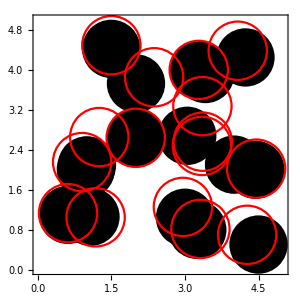
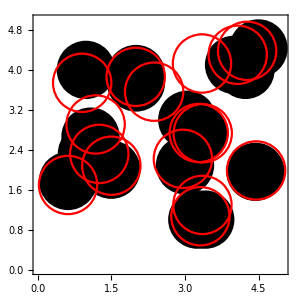
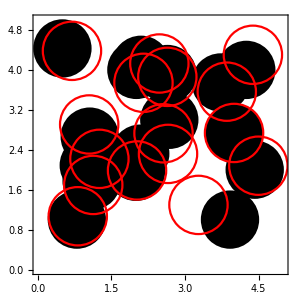

```mathematica
ShowSnapshot[10]
```

```mathematica
nn=Length[FileNames[bdir<>"snapshot_*"]];
Animate[ShowSnapshot[i],{i,0,nn-1,1},DisplayAllSteps->True]
```

```mathematica
nn=Length[FileNames[bdir<>"snapshot_*"]];
Manipulate[ShowSnapshot[i],{i,0,nn-1,1}]
```